```mathematica
(*DHplus=4.5 10^-9;(**)
DcG=9.4 10^^-11;(**)
brackE=3.645 10^-7;(**)
Kcat=1.6 10^3;(**)
Km=19;(**)
deltav=0.1;(**)
CHplus(*concentration of hydrogen ions*)
CG(*concentration of glucose*)
DHplus(*hydrogen ion diffusion coefficient*)
DcG(*diffusion coefficient of glucose*)
ET(*volume enzyme concentration*)
L(*thickness of theenzyme layer*)
Kcat(*kinetic enzyme reaction rate constant for glucose oxidation*)
Km(*Michaelis Menten constant*)
deltav(*dimensionless voltage drop across the cell*)
l(*distance between anode and cathode*)
y(*stoichhiometric coefficient*)
z(*coordinate direction normal to the anode (m)*)
t(*time (min)*)
Kc(*reaction rate constant at the cathode for the oxygen reduction reaction*)
O2(*concentration of oxygen*)*)
```

## Current-Voltage Modeling of the Enzymatic Glucose Fuel Cells

## PARAMETERs

```mathematica
L=0.005;(*thickness of an enzyme layer*)
G0=1;(*function of glucose concentration*)
Kcat=1000;(*kinetic enzyme raction rates*)
Km=0.019;(*kinetic enzyme raction rates*)
Et=10^-5;(*volume enzyme concentration*)
Es=L Et;(*surface enzyme concentration*)
DHplus=4.5 10^-9;(*diffusion coefficients of hydrogen ions*)
DG=9.4 10^^-11;(*diffusion coefficients of glucose ions*)
cHplus=;(*hydrogen ions concentration*)
ratio={2,1.25,1};(*ratio of DbHplus/DHplus*)
DbHplus=ratio DHplus;(*diffusion coefficients of hydrogen ions in the bulk solution*)
e=1.60217634 10^-19;(*electron charge*)
F=96485.4;(*Faraday constant*)
R=8.314;(*universal gas constant*)
T=300;(*temperature*)
EF=;(*electrical field*)
d=0.0035;(*distance the glucose concentration, unit: m*)
```

## FUNCTIONs

```mathematica
ClearAll[Es,g1s,HplusConcent,HplusConcent01,HplusConcent01x,ddHplusConcent01x,HplusKineticEqu02L,HplusConcent02L,GluKineticEqu01,HplusKineticEqu01,HplusKineticEqu,GluConcent,GluConcent01,GluConcent02,GluKineticEqu02,GluConent02L];
```

### Michaelis-Menten Equation

```mathematica
Es=Et L;
g1s=Kcat Es G[z]/(Km+G[z]);
```

### REGION: Electrode INTERFACE

#### Kinetics and Mass Transport for GLUCOSEN

ORIGINAL Expression

```mathematica
GluKineticEqu01=DG D[G[z],{z,2}]-2 (Kcat Et G[z])/(Km+G[z])==0;
GluConcent01=DSolve[{GluKineticEqu,G'[z]==-g1s/(2 DG)},G[z],z]
```

DSolve::deqn: Equation or list of equations expected instead of GluKineticEqu in the first argument {GluKineticEqu,G'[z]==-(Et Kcat L G[z])/(2 DG (Km+G[z]))}.

DSolve[{GluKineticEqu,G'[z]==-(Et Kcat L G[z])/(2 DG (Km+G[z]))},G[z],z]

APPROXIMATION Expression

```mathematica
GluKineticEqu02=DG D[G[z],{z,2}]-2 (Kcat Et G[z])/G[z]==0;
GluConcent02=DSolve[{GluKineticEqu02,G'[0]==-Kcat Es/(2 DG),G[0]==G0},G[z],z][[1,1,2]]//ExpandAll//FullSimplify
```

G0-(Et Kcat (L-2 z) z)/(2 DG)

```mathematica
Plot[Evaluate[y[z]/.GluConcent02],{z,0,1}]
```

ReplaceAll::reps: {-(Et Kcat (L-2 z) z)/(2 DG)+1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-(0.0000102143 Et Kcat (-0.0000408571+L))/DG+1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-(0.0102143 Et Kcat (-0.0408572+L))/DG+1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
GluKineticEqu03=DG D[G[z],{z,2}]-2 (Kcat Et G[z])/(Km+G[z])==0;
GluConcent03=NDSolve[{GluKineticEqu03,G'[z]==-g1s/(2 DG)},G[z],z]
```

#### Kinetics and Mass Transport for HYDROGEN

```mathematica
HplusKineticEqu01=DHplus D[Hplus[z],{z,2}]+2 (Kcat Et G0)/(Km+G0)==0;
HplusConcent01=DSolve[{HplusKineticEqu01,Hplus[0]==c0},Hplus[z],z][[1,1,2]]//ExpandAll//FullSimplify
```

c0+z (-(Et G0 Kcat z)/(DHplus (G0+Km))+C[2])

### REGION: Enzyme region

```mathematica
HplusConcent01x=HplusConcent01/.z->L;
ddHplusConcent01x=D[HplusConcent01,z]/.z->L;
GluConent02L=GluConcent02/.z->L;
HplusKineticEqu02L=DbHplus D[Hplus[z],{z,2}]==0;
HplusConcent02L=DSolve[{HplusKineticEqu02L,Hplus[d]==cd},Hplus[z],z][[1,1,2]]//ExpandAll//FullSimplify
HplusConcent02Lx=HplusConcent02L/.z->L;
ddHplusConcent02Lx=DbHplus D[HplusConcent02L,z]/.z->L;
eq1=HplusConcent01x==HplusConcent02Lx;
eq2=ddHplusConcent01x==ddHplusConcent02Lx;
c1=Solve[eq1&&eq2,{C[1],C[2]}][[1,1,2]]//ExpandAll//FullSimplify
c2=Solve[eq1&&eq2,{C[1],C[2]}][[1,2,2]]//ExpandAll//FullSimplify
```

(cd z+(d-z) C[1])/d

(c0 d DHplus (G0+Km)+L (cd (-1+DbHplus) DHplus (G0+Km)+d Et G0 Kcat L))/(DHplus (G0+Km) (d+(-1+DbHplus) L))

(-c0 DbHplus DHplus (G0+Km)+cd DbHplus DHplus (G0+Km)+Et G0 Kcat L (2 d+(-2+DbHplus) L))/(DHplus (G0+Km) (d+(-1+DbHplus) L))

### Current Density of Hydrogen Ions jHplus

```mathematica
jHplus[]:=-e DHplus D[cHplus,x](*+e (F DHplus cHplus)/(R T) EF*)
```

```mathematica
s=NDSolve[{y''[x]+ Sin[y[x]]y[x]==0,y[0]==1,y'[0]==0},y,{x,0,30}];
Plot[Evaluate[{y[x],y'[x],y''[x]}/.s],{x,0,30},PlotStyle->Automatic];
```

## Perturbation Method

## ClearAll

```mathematica
Clear["`*"]
```

## Physical Constant

```mathematica
CatalystConstant=10^3;(*Kinetic Enzyme Reaction Rate [Subscript[K, cat]], "Sec^-1"*)
MMConstant=0.019;(*Kinetic Enzyme Reaction Rate [Subscript[K, M]], "M"*)
TotalEnzymeConcentraton=0.1 10^-5;(*{0.7 10^-5,0.5 10^-5,0.3 10^-5,0.1 10^-5}*)(*Volume Enzyme Concentration [Subscript[E, T]], "M"*)
L=0.001;(*Thickness of an Enzyme Layer [L], "m"*)
d=0.003;(*Distance Between Electrodes [d], "m"*)
GlucoseIonDiffusionCoefficient=10^-5;(*Diffusion Coefficients of Glucose [Subscript[D, G]], "m^2s^-1"*)
HydrogenIonDiffusionCoefficient=10^-5;(*Diffusion Coefficients of Hydrogen Ions [D_(H+)], "m^2s^-1"*)
BulkHydrogenIonDiffusionCoefficient=10^-5;(*Diffusion Coefficient of Hydrogen Ions in Bulk [D_(bH+)], "m^2s^-1"*)
HydrogenConcentrationX0=0.002;(*Hydrogen Ions Concentration Between the Glucose Reservoir and an Anode [Subscript[c, 0]], "M"*)
GlucoseConcentrationX0=1;(*{0.001,0.01,0.1,0.19,1.9};*)(*Glucose Concentration in the Glucose Reservoir [Subscript[G, 0]], "mol/m^3"*)
SurfaceEnzymeConcentration=TotalEnzymeConcentraton L;(**)
HydrogenConcentration[X];
GlucoseConcentration[X];(*={0.1,0.01,0.001}*)(*Glucose Concentration [G], "M"*)
```

## Dimensionless Form

```mathematica
CH[X_]=HydrogenConcentration[X]/HydrogenConcentrationX0
G[X_]=GlucoseConcentration[X]/GlucoseConcentrationX0
(*X=x/d;*)
Ci=GlucoseConcentrationX0/HydrogenConcentrationX0;
α=(2 d^2 CatalystConstant TotalEnzymeConcentraton)/(GlucoseIonDiffusionCoefficient MMConstant);
β=GlucoseConcentrationX0/MMConstant;
ξ1=GlucoseIonDiffusionCoefficient/HydrogenIonDiffusionCoefficient;
ξ2=HydrogenIonDiffusionCoefficient/BulkHydrogenIonDiffusionCoefficient;
g1s[X_]:=(CatalystConstant SurfaceEnzymeConcentration GlucoseConcentration[X])/(MMConstant+GlucoseConcentration[X]);
z=2;
```

500. HydrogenConcentration[X]

GlucoseConcentration[X]

## Non-linear Differential Equations for Direct Transport

```mathematica
FindRoot[{DSolve[{G''[X]+(α G[X])/(1+β G[X])==0,G'[0]==(-α L)/(2 d z (1+β))},G[X],X]},{X,0}];
DSolve[{CH''[X]+(α ξ1 Ci G[X])/(1+β G[X])==0},CH[X],X];
```

### Glucose Concentration

```mathematica
Plot[Evaluate[NDSolve[{G''[X]+(α G[X])/(1+β G[X])==0,G'[0]==(-α L)/(2 d z (1+β)),G[0]==1},G[X],{X,0,1}]],{X,0,1},PlotRange->All];
```

```mathematica
Plot[Evaluate[G[x]/.NDSolve[{G''[x]+(α G[x])/(1+β G[x])==0,G'[0]==(-α L)/(2 d z (1+β)),G[0]==1},G[x],x]],{x,0,1}];
sol=NDSolve[{G''[x]-(α G[x])/(1+β G[x])==0,G[0]==1,G'[0]==(-α L)/(2 d z (1+β))},G[x],x];Plot[G[x]/.sol,{x,0,1}];
```

### Hydrogen Concentration

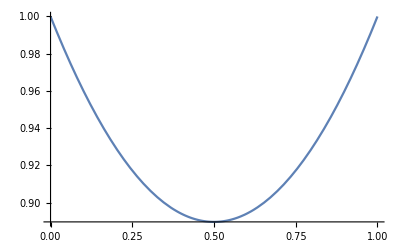

```mathematica
num=Plot[Evaluate[Ch[x]/.NDSolve[{Ch''[x]-(α ξ1 Ci G[x])/(1+β G[x])==0,Ch[1]==1,Ch[0]==1,G''[x]+(α G[x])/(1+β G[x])==0,G'[0]==(-α L)/(2 d z (1+β)),G[0]==1},{Ch[x],G[x]},x]],{x,0,1}]
```

### Hydrogen Concentration Approximation

```mathematica
Plot[Evaluate[Ch[x]/.NDSolve[{Ch''[x]-(α ξ1 Ci)/(1+β)==0,Ch[1]==1,Ch[0]==1},Ch[x],x]],{x,0,1}];
```

NDSolve::ndlim: Range specification x is not of the form {x, xend} or {x, xmin, xmax}.

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

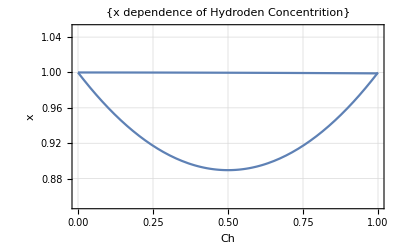

```mathematica
Show[{Plot[Evaluate[G[x]/.NDSolve[{G''[x]+(α G[x])/(1+β G[x])==0,G'[0]==(-α L)/(2 d z (1+β)),G[0]==1},G[x],x]],{x,0,1}],Plot[Evaluate[Ch[x]/.NDSolve[{Ch''[x]-(α ξ1 Ci)/(1+β)==0,Ch[1]==1,Ch[0]==1},Ch[x],x]],{x,0,1}]},PlotRange->{{0,1},{.85,1.05}},Frame->True,PlotStyle->{{Red},{Black,Dashed}},PlotLabel->{"x dependence of Hydroden Concentrition"},GridLines->Automatic,PlotLegends->{"G","Ch"},AxesLabel->{Ch,x}]
```

### Comparison between Num, Ana, Diff Calculation

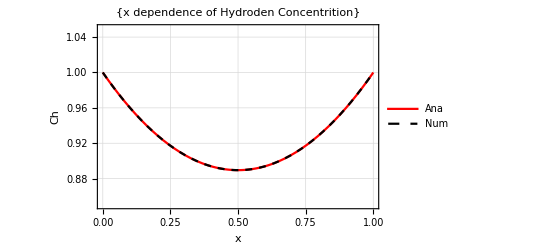

```mathematica
Plot[{1/2 (α ξ1 Ci)/(1+β) (x-0.5)^2+1-(α ξ1 Ci)/(1+β) 1/8,Evaluate[Ch[x]/.NDSolve[{Ch''[x]-(α ξ1 Ci G[x])/(1+β G[x])==0,Ch[1]==1,Ch[0]==1,G''[x]+(α G[x])/(1+β G[x])==0,G'[0]==(-α L)/(2 d z (1+β)),G[0]==1},{Ch[x],G[x]},x]]},{x,0,1},PlotRange->{{0,1},{.85,1.05}},PlotLegends->{"Ana","Num"},Frame->True,PlotStyle->{{Red},{Black,Dashed}},PlotLabel->{"x dependence of Hydroden Concentrition"},AxesLabel->{x,Ch},GridLines->Automatic]
```

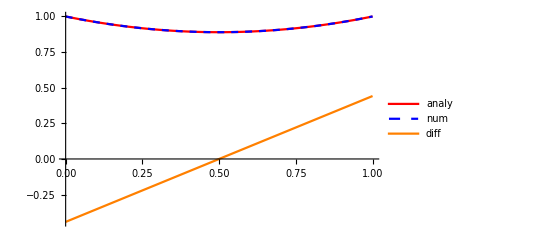

```mathematica
DSolve[c''[x]-a==0,c[x],x];Plot[{1/2 (α ξ1 Ci)/(1+β) (x-0.5)^2+1-(α ξ1 Ci)/(1+β) 1/8},{x,0,1}];
Plot[{Evaluate[Ch[x]/.NDSolve[{Ch''[x]-(α ξ1 Ci)/(1+β)==0,Ch[1]==1,Ch[0]==1},Ch[x],x]],1/2 (α ξ1 Ci)/(1+β) (x-0.5)^2+1-(α ξ1 Ci)/(1+β) 1/8,(α ξ1 Ci)/(1+β) x-1/2 (α ξ1 Ci)/(1+β)},{x,0,1},PlotLegends->{"analy","num","diff"},PlotStyle->{Red,{Dashed,Blue},Orange}]
```

## TEST

```mathematica
dG[x_]:=D[G[x],x]
d2G[x_]:=D[G[x],{x,2}]
GKEqu=d2G[x]-2 Kcat Et G[x]/(Km+G[x])==0
GBEqu1=dG[0]==-g1s/DG
GBEqu2=G[0]==G0
GCEqu=NDSolve[{GKEqu,GBEqu1,GBEqu2},G[x],x]
```

-(2 Et Kcat G[x])/(Km+G[x])+G''[x]==0

General::ivar: 0 is not a valid variable.

∂_0 G[0]==-g1s/DG

G[0]==G0

NDSolve::ndlim: Range specification x is not of the form {x, xend} or {x, xmin, xmax}.

General::ivar: 0 is not a valid variable.

NDSolve::ndinnt: Initial condition G0 is not a number or a rectangular array of numbers.

NDSolve[{-(2 Et Kcat G[x])/(Km+G[x])+G''[x]==0,∂_0 G[0]==-g1s/DG,G[0]==G0},G[x],x]

```mathematica
beta=G0/KM;Gbar=G/G0;cHbar=cH/c0;xbar=x/d;ξ1=DG/DH;ξ2=DH/DbH;ci=G0/c0;
alpha=(2 d^2 Kcat Et)/(DG KM);beta Gbar;G/KM;(Gbar/xbar)^-1 Kcat Et G/(KM+G) 1/(z DG);
alpha/(2 d z (1+beta))
```

(Et G0 Kcat x)/(d DG (G+KM) z)

(d Et Kcat)/(DG (1+G0/KM) KM z)

```mathematica
diffeq=G''[x]-(α G[x])/(1+β G[x])==0;
DSolve[{diffeq,G[0]==G0,G'[0]==g0},G[x],x]
```

DSolve::bvimp: General solution contains implicit solutions. In the boundary value problem, these solutions will be ignored, so some of the solutions will be lost.

{}

{{y[x]→InterpolatingFunction[…][x]}}

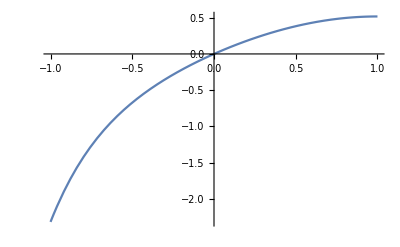

```mathematica
solution=NDSolve[{y'''[x]+3 y''[x]+2 y'[x]+6 y[x]==0,y[0]==0,y'[0]==1,y''[0]==-1},y[x],{x,-1,1}]
Plot[y[x]/.solution,{x,-1,1},PlotRange->All]
```

```mathematica
eq1=1/r1+1/(r2+r3+r4)==1/r11;
eq2=1/r2+1/(r1+r3+r4)==1/r22;
eq3=1/r3+1/(r2+r1+r4)==1/r33;
eq4=1/r4+1/(r2+r3+r1)==1/r44;
eq5=1/(r1+r2)+1/(r3+r4)==1/r12;
eq6=1/(r1+r4)+1/(r2+r3)==1/r13;
Solve[{eq1&&eq2&&eq3&&eq4&&eq5&&eq6&&r11>0&&r22>0&&r33>0&&r44>0&&r12>0&&r13>0},{r1,r2,r3,r4},NonNegativeReals]
```

$Aborted